```mathematica
$Version
Clear["Global`*"];
ineq1 = ((1+γ+γ^2) r[4]<r[2]+γ (γ r[1]+r[3])||r[2]+γ r[3]≤(1+γ) r[1])&&(γ (r[1]-r[2]-(1+γ) (r[3]-r[4]))+r[4]<r[2]||r[2]+γ r[3]>(1+γ) r[1]);
eq1 = r[1]/(1-γ^3)+(γ r[2])/(1-γ^3)+(γ^2 r[3])/(1-γ^3);
reg1=ImplicitRegion[ineq1,{{r[1],0,1},{r[2],0,1},{r[3],0,1},{r[4],0,1}}];
(int[y_]=Assuming[1>y>0,Integrate[1,{r[1],r[2],r[3],r[4],r[5]}∈reg1]//Simplify])//AbsoluteTiming
(int[y_]=Assuming[1>y>0,Integrate[eq1,{r[1],r[2],r[3],r[4],r[5]}∈reg1]//Simplify])//AbsoluteTiming
```

12.0.0 for Linux x86 (64-bit) (April 7, 2019)

```mathematica
(int[y_]=Assuming[1>y>0,Integrate[1,{r[1],r[2],r[3],r[4],r[5]}∈reg1]//Simplify])//AbsoluteTiming

funcs={int[y][[1,1,1]],int[y][[1,2,1]],int[y][[2]]}
```

```mathematica
{(-6-8 y+y^2+4 y^3+6 y^4+4 y^5)/(24 (-1+y) (1+y)^2),(1-4 y+9 y^2+12 y^3+3 y^4-y^6)/(24 y^2 (1+y)),-(1-10 y^2-12 y^3+15 y^4+48 y^5+36 y^6-24 y^7-59 y^8-24 y^9+28 y^10+20 y^11-13 y^12-12 y^13+2 y^14+4 y^15+y^16)/(24 (-1+y) y^2 (1+y)^2)}
```

```mathematica
Simplify[!2*y≥1&&!(Sqrt[5]+2*y<3||(Sqrt[5]+2*y>3&&2*y<1))]
sol=Solve[%,y][[1]]
Equal@@funcs[[1;;2]]/.y->1/2
Equal@@funcs[[2;;3]]/.y->(3-Sqrt[5])/2//Simplify
funcs[[1]]
```

```mathematica
√5+2 y==3
```

```mathematica
{y->1/2 (3-√5)}
```

True

True

```mathematica
(-1+6 y+y^2+2 y^4)/(24 y^2)
```

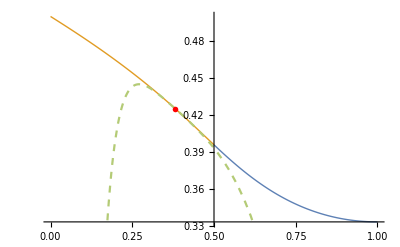

```mathematica
Show[Plot[funcs[[1]],{y,1/2,1},PlotStyle->{{Thick,ColorData[97][1]}}],Plot[funcs[[2]],{y,0,1/2},PlotStyle->{{Thick,ColorData[97][2]}}],Plot[funcs[[3]],{y,0,1},PlotStyle->{{Dashed,Lighter@ColorData[97][3]}}],PlotRange->{{0,1},{int[1],int[0]}},Epilog->{Red,AbsolutePointSize[4],Point[{y,int[y]}/.sol]}]
```